```mathematica
ClearAll["Global`*"]
```

### Graph G_1

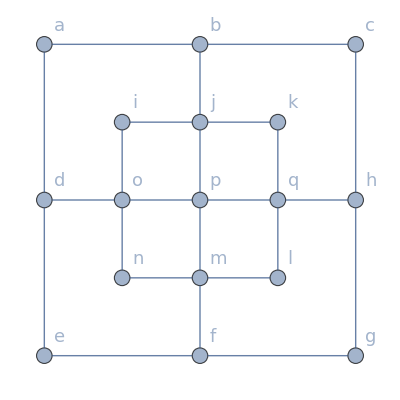

```mathematica
G1=Graph[
{"a"<->"b", "a"<->"d",
"b"<->"c", "b"<->"j",
"c"<->"h",
"d"<->"o","d"<->"e",
"e"<->"f",
"f"<->"m","f"<->"g",
"g"<->"h",
"h"<->"q",
"i"<->"j","i"<->"o",
"j"<->"p","j"<->"k",
"k"<->"q",
"l"<->"q","l"<->"m",
"m"<-> "n","m"<->"p",
"n"<->"o",
"o"<->"p",
"p"<->"q"},
VertexLabels->"Name",VertexLabelStyle->Directive[FontSize->18,Italic],VertexSize->Medium,EdgeStyle->Thick,
VertexCoordinates->{
"a"->{-2, 2}, "b"->{0,2},
"c"->{2,2},"d"->{-2,0},
"e"->{-2,-2},"f"->{0,-2},
"g"->{2,-2},"h"->{2,0},
"i"->{-1,1},"j"->{0,1},"k"->{1,1},
"l"->{1,-1},"m"->{0,-1},"n"->{-1,-1},
"o"->{-1,0},"p"->{0,0},"q"->{1,0}}]
```

```mathematica
FindHamiltonianCycle[G1]
```

{}

### Graph G_2

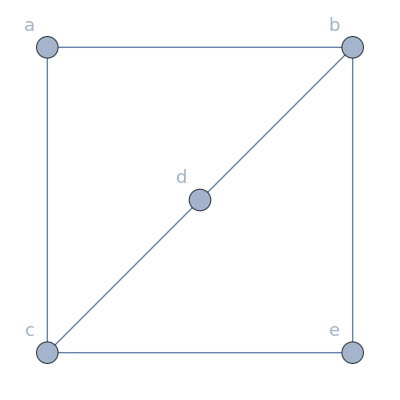

```mathematica
G2=Graph[{
"a"<->"b","a"<->"c","b"<->"d","b"<->"e","c"<->"d","c"<->"e"},
VertexLabels->Placed["Name",{Before,Above}],
VertexLabelStyle->Directive[FontSize->18,Italic],VertexSize->Small,EdgeStyle->Thick,
VertexCoordinates->{"a"->{0,2},"b"->{2,2},"c"->{0,0},"d"->{1,1},"e"->{2,0}}]
```

```mathematica
FindHamiltonianCycle[G2]
```

{}

### Graph G_3

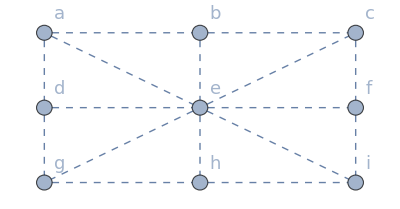

```mathematica
G3=Graph[{
"a"<->"b","a"<->"d","a"<->"e",
"b"<->"c","b"<->"e",
"c"<->"e","c"<->"f",
"d"<->"e","d"<->"g",
"e"<->"f","e"<->"g","e"<->"h","e"<->"i",
"f"<->"i",
"g"<->"h",
"h"<->"i"},
VertexLabels->"Name",
VertexLabelStyle->Directive[FontSize->18,Italic],
VertexSize->Medium,EdgeStyle->Dashed,
VertexCoordinates->{
"a"->{-2,1},"b"->{0,1},"c"->{2,1},
"d"->{-2,0},"e"->{0,0},"f"->{2,0},
"g"->{-2,-1},"h"->{0,-1},"i"->{2,-1}}]
```

```mathematica
HCycles=FindHamiltonianCycle[G3,100]
```

{{a<->b,b<->c,c<->f,f<->i,i<->e,e<->h,h<->g,g<->d,d<->a},{a<->b,b<->c,c<->f,f<->e,e<->i,i<->h,h<->g,g<->d,d<->a},{a<->d,d<->g,g<->e,e<->h,h<->i,i<->f,f<->c,c<->b,b<->a},{a<->b,b<->c,c<->e,e<->f,f<->i,i<->h,h<->g,g<->d,d<->a},{a<->d,d<->e,e<->g,g<->h,h<->i,i<->f,f<->c,c<->b,b<->a},{a<->b,b<->e,e<->c,c<->f,f<->i,i<->h,h<->g,g<->d,d<->a},{a<->b,b<->c,c<->f,f<->i,i<->h,h<->g,g<->d,d<->e,e<->a},{a<->e,e<->b,b<->c,c<->f,f<->i,i<->h,h<->g,g<->d,d<->a}}

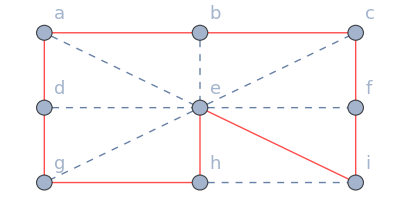
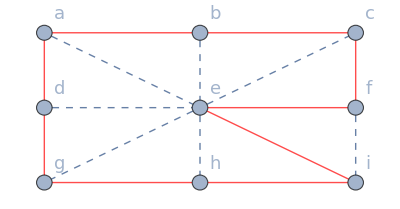
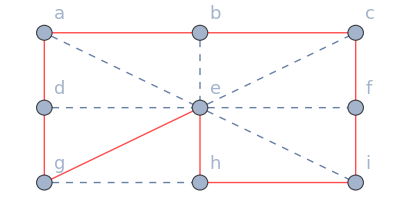
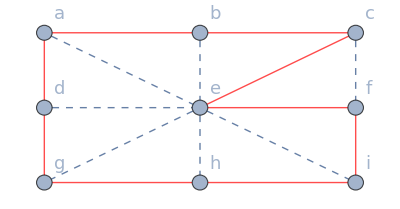
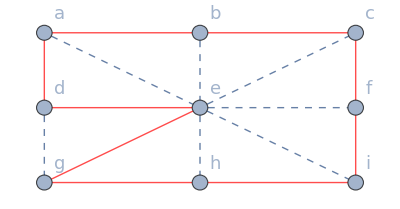
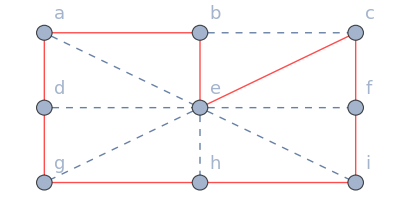
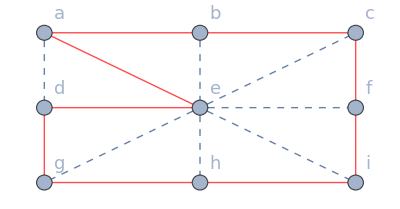
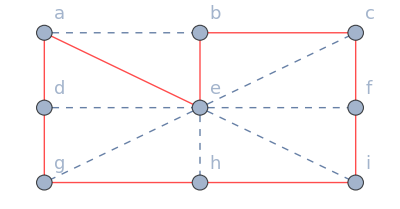

```mathematica
Table[HighlightGraph[G3,
Style[#,Directive[Red,Dashing[{}]],Thick]&/@HCycles[[i]]],{i,1,8}]
```